```mathematica
setVariables[]
ΔE = 10000;
UbaseLab = MatrixExp[-ⅈ*t*(HexactStatic // Diagonal // DiagonalMatrix) // N];
clearVariables[]
```

```mathematica
swapOrder[M_] := M[[{2, 1}, {2, 1}]]
```

### Core gate Here I define the core, sweeping gate that gives a charge-noise resistant ϕx, but not charge-noise resistant ϕzs

```mathematica
(* runs a core (sweep) gate, with ΔE error δE, with the driving fields attenuated by λ *)
coreGateByλ[λ_, δE_] := (
setVariables[];

T1 = 5*10^-9;
T2 = 110*10^-9;
Tmax = 2*T1 + T2;

ΔEMid = 0;

Clear[Eamp, Bamp];

(*Ea =244;
Ba = .0318;

ωE = 3.3767399946666843*^10;
ωB = 3.365817946982966*^10;

Eamp[t_] := λ*Ea*cosWindow[t - T1, T2/5, T2];
Bamp[t_] := λ*Ba*cosWindow[t - T1, T2/5, T2];*)

Ea =255.2;
Ba = 0.03326;

ωE = 3.37094*^10;
ωB = 3.36003*^10;

Eamp[t_] := λ*Ea*cosWindow[t - T1, T2/5, T2]^2;
Bamp[t_] := λ*Ba*cosWindow[t - T1, T2/5, T2]^2;

ΔE = 10000 - 12000*twoPointWindow[t, T1, Tmax, 8/12] + δE;

U = findEvolutionOperator2D[Hexact, Tmax];
UU = U /. t->Tmax;

clearVariables[];

UU
)

(* note that the ϕx that a given λ gives is a priori unknown.  here I numerically find ϕx(λ) and redefine the core gate function *)
coreCalData = Table[{gateDecompositionParameters[coreGateByλ[λ, 0]][[2]], λ}, {λ, 0, 1, .05}];
ϕxFunction = Interpolation[coreCalData, Method->"Spline"];
coreGate[ϕx_, δE_] := coreGateByλ[ϕxFunction[ϕx], δE]
```

```mathematica
(* quick check for Ed *)
Ux = coreGateByλ[1, 0]
UxNaive = naiveCoreGateByλ[1, 0]
```

```mathematica
Ux // gateDecompositionParameters
1 - fidelity2D[MatrixExp[-ⅈ*%[[2]]*σX/2], σX]
UxNaive // gateDecompositionParameters
1 - fidelity2D[MatrixExp[-ⅈ*%[[2]]*σX/2], σX]
```

{0.610519,3.13231,0.34875,4.81462,0.999996}

0.000014366

{0.637465,3.13391,1.88863,0.68209,0.999991}

9.82522×10^-6

#### Core gate - primes To know the right parameters for the echo sequence, I here numerically calculate the derivatives of the two ϕz angles w.r.t. δE

```mathematica
Clear[coreGateϕzPrimes]
coreGateϕzPrimes[ϕx_] := Module[{paramsA, paramsB, Δϕz1, Δϕz2}, (
paramsA = coreGate[ϕx, -25] // gateDecompositionParameters;
(*Print[paramsA];*)
paramsB = coreGate[ϕx, 25] // gateDecompositionParameters;
(*Print[paramsB];*)
Δϕz1 = paramsB[[1]] - paramsA[[1]];
If[Δϕz1 > π, Δϕz1 = Δϕz1 - 2π];
If[Δϕz1 < -π, Δϕz1 = Δϕz1 + 2π];
Δϕz2 = paramsB[[3]] - paramsA[[3]];
If[Δϕz2 > π, Δϕz2 = Δϕz2 - 2π];
If[Δϕz2 < -π, Δϕz2 = Δϕz2 + 2π];
{Δϕz1, Δϕz2}/50
)]

coreGateϕzPrimeData = Table[{ϕx, coreGateϕzPrimes[ϕx]}, {ϕx, π/20, 19π/20, π/20}];
coreGatePrimeFunction = Interpolation[coreGateϕzPrimeData, Method->"Spline"];
```

$Aborted

Interpolation::innd: First argument in coreGateϕzPrimeData does not contain a list of data and coordinates.

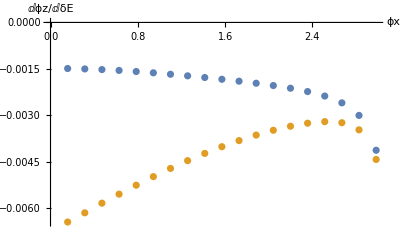

```mathematica
ListPlot[{Table[{x[[1]], x[[2]][[1]]}, {x, coreGateϕzPrimeData}], Table[{x[[1]], x[[2]][[2]]}, {x, coreGateϕzPrimeData}]}, AxesLabel->{"ϕx", "ⅆϕz/ⅆδE"}]
```

### R_z(ϕ_z) Here I define an Rz gate in a similar way to an Rx gate. I first define it in terms of a physical input (not attenuation λ, here, but instead duration T) and then back-solve to find ϕz(T)

```mathematica
RzAngle[U_] := ArcTan[Re[U[[2, 2]]/U[[1, 1]]], Im[U[[2, 2]]/U[[1, 1]]]]
unravel[input_] := (
output = input;
Do[(
If[output[[i + 1]] - output[[i]] > π, output[[i + 1;;]] = output[[i + 1;;]] - 2π];
If[output[[i + 1]] - output[[i]] < -π, output[[i + 1;;]] = output[[i + 1;;]] + 2π];
),{i, Length[input] - 1}
];
output
)

RzByTime[T_?NumericQ,δE_] := (
statusString = "Rz; Error of " <> ToString[δE] <> "V/m"; 

setVariables[];

Eamp[t_] := 0;
Bamp[t_] := 0;
Tmax = T;
T1 = Min[5*10^-9, Tmax/2];
T2 = Tmax - 2*T1;
ΔΔE = 20000*Min[1, T1/(5*10^-9)];
ΔE =10000 - ΔΔE*cosWindow[t, T1, Tmax] + δE // N;

U= findEvolutionOperator2D[Hexact, Tmax];

UU = U /. t->Tmax;

clearVariables[];

UU
)

RzCalData = Table[{RzAngle[RzByTime[tt, 0]], tt}, {tt, 0, 25*10^-9, 1*10^-9}];
RzCalData[[All, 1]] = unravel[RzCalData[[All, 1]]];
ϕzFunction = Interpolation[RzCalData, Method->"Spline"];
Rz[ϕz_, δE_] := RzByTime[ϕzFunction[ϕz], δE]
```

### Echo Rz Define a noise-vulnerable Rz gate that acts to echo away linear Rz errors

```mathematica
Clear[echoRzByTime]
echoRzByTime[T_?NumericQ,δE_] := (
statusString = "echo Rz; Error of " <> ToString[δE] <> "V/m"; 

setVariables[];

Eamp[t_] := 0;
Bamp[t_] := 0;
Tmax = T;
T1 = Min[2*10^-9, Tmax/2];
T2 = Tmax - 2*T1;
ΔΔE = 10000*Min[1, T1/(2*10^-9)];
ΔE =10000 - ΔΔE*cosWindow[t, T1, Tmax] + δE // N;

U= findEvolutionOperator2D[Hexact, Tmax];

UU = U /. t->Tmax;

clearVariables[];

UU
)

echoϕzPrimeByTime[T_] := Module[{ϕzA, ϕzB},(
ϕzA = RzAngle[echoRzByTime[T, -25]];
ϕzB = RzAngle[echoRzByTime[T, 25]];
Mod[(ϕzB - ϕzA)/50 + π, 2π] - π
)]

echoϕzPrimeCalData = Table[{echoϕzPrimeByTime[tt], tt}, {tt, 0, 50*10^-9, 1*10^-9}];
echoϕzPrimeFunction = Interpolation[echoϕzPrimeCalData, Method->"Spline"];
echoRz[ϕzPrime_, δE_] := echoRzByTime[echoϕzPrimeFunction[ϕzPrime], δE]
```

### For comparison, solve for a naive gate in a similar time to the sweeping gate with no sweep and no echo

```mathematica
naiveCoreGateByλ[λ_, δE_] := (
setVariables[];
T1 = 5*10^-9;
T2 = 100*10^-9;
Tmax = 2*T1 + T2;

Clear[Eamp, Bamp];
Ea =λ*112.68229305101102;
ωE = 3.389283961963769*^10;
Eamp[t_] := Ea*cosWindow[t - T1, T2/3, T2];
Ba = λ*0.014612579500812886;
ωB = 3.37328583857908*^10;
Bamp[t_] := Ba*cosWindow[t - T1, T2/3, T2];

ΔE = 10000 - 10000*twoPointWindow[t, T1, Tmax, 1] + δE;

U = findEvolutionOperator2D[Hexact, Tmax];
UU = U /. t->Tmax;

clearVariables[];

UU
)

naiveCalData = Table[{gateDecompositionParameters[naiveCoreGateByλ[λ, 0]][[2]], λ}, {λ, 0, 1, .05}];
naiveϕxFunction = Interpolation[naiveCalData, Method->"Spline"];
naiveCoreGate[ϕx_, δE_] := naiveCoreGateByλ[naiveϕxFunction[ϕx], δE]
```

```mathematica
naiveCalData
naiveCoreGate[π/2, 0]
%//gateDecompositionParameters
```

{{0.,0.},{0.010401,0.05},{0.0416769,0.1},{0.0939935,0.15},{0.16747,0.2},{0.261997,0.25},{0.377081,0.3},{0.511737,0.35},{0.664485,0.4},{0.833417,0.45},{1.01632,0.5},{1.21082,0.55},{1.41448,0.6},{1.625,0.65},{1.84021,0.7},{2.05814,0.75},{2.27711,0.8},{2.49562,0.85},{2.71248,0.9},{2.92661,0.95},{3.13391,1.}}

{{0.151515+0.690682 ⅈ,0.380201+0.596192 ⅈ},{0.685406-0.173828 ⅈ,-0.58355+0.399331 ⅈ}}

{6.25076,1.5708,1.21905,5.08975,0.999994}

### Find κ angles to apply to leave only Rx(ϕx)

```mathematica
findκs[ϕxTar_]:=
Module[{primes, echoU1, echoU2, X1U, X2U, coreU, totalT, Rzϕz1, Rzϕz2, Rz1U, Rz2U, fullU, errϕz1, errϕz2}, (
primes = coreGatePrimeFunction[ϕxTar];

echoU1 = echoRz[primes[[1]], 0];
X1U = coreGate[π, 0];
coreU = coreGate[ϕxTar, 0];
X2U = coreGate[π, 0];
echoU2 = echoRz[primes[[2]], 0];

(* find ϕz angles without Rz gates *)
totalT = echoϕzPrimeFunction[primes[[1]]] + 3*120*10^-9 + echoϕzPrimeFunction[primes[[2]]];
fullU = ConjugateTranspose[UbaseLab[[{1, 2}, {1, 2}]] /. t->totalT].echoU1.X1U.coreU.X2U.echoU2;
errϕz1 = gateDecompositionParameters[fullU][[1]];
errϕz2 = gateDecompositionParameters[fullU][[3]];

Rzϕz1 = Mod[-errϕz1 - .5, 2π] + .5;
Rzϕz2 = Mod[-errϕz2, 2π];
Rzϕz1 = Rzϕz1 + 2.4*10^7*(ϕzFunction[Rzϕz1] + ϕzFunction[Rzϕz2]);

Rz1U = Rz[Rzϕz1, 0];
Rz2U = Rz[Rzϕz2, 0];

totalT = ϕzFunction[Rzϕz1] + echoϕzPrimeFunction[primes[[1]]] + 3*120*10^-9 + echoϕzPrimeFunction[primes[[2]]] + ϕzFunction[Rzϕz2];
fullU = ConjugateTranspose[UbaseLab[[{1, 2}, {1, 2}]] /. t->totalT].Rz1U.echoU1.X1U.coreU.X2U.echoU2.Rz2U;
Print[fullU // gateDecompositionParameters];

{Rzϕz1, Rzϕz2}
)]

findκsNoEcho[ϕxTar_]:=
Module[{primes, echoU1, echoU2, X1U, X2U, coreU, totalT, Rzϕz1, Rzϕz2, Rz1U, Rz2U, fullU, errϕz1, errϕz2}, (

coreU = coreGate[ϕxTar, 0];

(* find ϕz angles without Rz gates *)
totalT = 120*10^-9;
fullU = ConjugateTranspose[UbaseLab[[{1, 2}, {1, 2}]] /. t->totalT].coreU;
errϕz1 = gateDecompositionParameters[fullU][[1]];
errϕz2 = gateDecompositionParameters[fullU][[3]];

Rzϕz1 = Mod[-errϕz1 - .5, 2π] + .5;
Rzϕz2 = Mod[-errϕz2, 2π];
Rzϕz1 = Rzϕz1 + 2.4*10^7*(ϕzFunction[Rzϕz1] + ϕzFunction[Rzϕz2]);

Rz1U = Rz[Rzϕz1, 0];
Rz2U = Rz[Rzϕz2, 0];

totalT = ϕzFunction[κs[[1]]] + 120*10^-9 + ϕzFunction[κs[[2]]];
fullU = ConjugateTranspose[UbaseLab[[{1, 2}, {1, 2}]] /. t->totalT].Rz1U.coreU.Rz2U;
Print[fullU // gateDecompositionParameters];

{Rzϕz1, Rzϕz2}
)]

findκsNaive[ϕxTar_]:=
Module[{primes, echoU1, echoU2, X1U, X2U, coreU, totalT, Rzϕz1, Rzϕz2, Rz1U, Rz2U, fullU, errϕz1, errϕz2}, (

coreU = naiveCoreGate[ϕxTar, 0];

(* find ϕz angles without Rz gates *)
totalT = 110*10^-9;
fullU = ConjugateTranspose[UbaseLab[[{1, 2}, {1, 2}]] /. t->totalT].coreU;
errϕz1 = gateDecompositionParameters[fullU][[1]];
errϕz2 = gateDecompositionParameters[fullU][[3]];

Rzϕz1 = Mod[-errϕz1 - .5, 2π] + .5;
Rzϕz2 = Mod[-errϕz2, 2π];
Rzϕz1 = Rzϕz1 + 2.4*10^7*(ϕzFunction[Rzϕz1] + ϕzFunction[Rzϕz2]);

Rz1U = Rz[Rzϕz1, 0];
Rz2U = Rz[Rzϕz2, 0];

totalT = ϕzFunction[κs[[1]]] + 120*10^-9 + ϕzFunction[κs[[2]]];
fullU = ConjugateTranspose[UbaseLab[[{1, 2}, {1, 2}]] /. t->totalT].Rz1U.coreU.Rz2U;
Print[fullU // gateDecompositionParameters];

{Rzϕz1, Rzϕz2}
)]
```

### Solve full, Rz-removed gates

```mathematica
(* returns U *)
RxGate[ϕxTar_, δE_, κs_]:=
Module[{primes, echoU1, echoU2, X1U, X2U, coreU, totalT, Rzϕz1, Rzϕz2, Rz1U, Rz2U, fullU, errϕz1, errϕz2}, (
primes = coreGatePrimeFunction[ϕxTar];

Rz1U = Rz[κs[[1]], δE];
echoU1 = echoRz[primes[[1]], δE];
X1U = coreGate[π, δE];
coreU = coreGate[ϕxTar, δE];
X2U = coreGate[π, δE];
echoU2 = echoRz[primes[[2]], δE];
Rz2U = Rz[κs[[2]], δE];

totalT = ϕzFunction[κs[[1]]] + echoϕzPrimeFunction[primes[[1]]] + 3*120*10^-9 + echoϕzPrimeFunction[primes[[2]]] + ϕzFunction[κs[[2]]];
fullU = ConjugateTranspose[UbaseLab[[{1, 2}, {1, 2}]] /. t->totalT].Rz1U.echoU1.X1U.coreU.X2U.echoU2.Rz2U;

(*Print[δE];
Print[fullU//gateDecompositionParameters];*)

fullU
)]

RxGateNoEcho[ϕxTar_, δE_, κs_]:=
Module[{primes, echoU1, echoU2, X1U, X2U, coreU, totalT, Rzϕz1, Rzϕz2, Rz1U, Rz2U, fullU, errϕz1, errϕz2}, (

Rz1U = Rz[κs[[1]], δE];
coreU = coreGate[ϕxTar, δE];
Rz2U = Rz[κs[[2]], δE];

totalT = ϕzFunction[κs[[1]]] + 120*10^-9 + ϕzFunction[κs[[2]]];
fullU = ConjugateTranspose[UbaseLab[[{1, 2}, {1, 2}]] /. t->totalT].Rz1U.coreU.Rz2U;

fullU
)]

RxGateNaive[ϕxTar_, δE_, κs_]:=
Module[{primes, echoU1, echoU2, X1U, X2U, coreU, totalT, Rzϕz1, Rzϕz2, Rz1U, Rz2U, fullU, errϕz1, errϕz2}, (

Rz1U = Rz[κs[[1]], δE];
coreU = naiveCoreGate[ϕxTar, δE];
Rz2U = Rz[κs[[2]], δE];

totalT = ϕzFunction[κs[[1]]] + 110*10^-9 + ϕzFunction[κs[[2]]];
fullU = ConjugateTranspose[UbaseLab[[{1, 2}, {1, 2}]] /. t->totalT].Rz1U.coreU.Rz2U;

fullU
)]
```